```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
H[k_,q_]:=(-μ-Cos[k]Cos[q])σ3-Sin[k]Sin[q]σ0+Δ Sin[k]σ2
evals[k_,q_]:=Eigenvalues[H[k,q]]
```

```mathematica
Animate[
Plot[evals[k,q]/.{μ->0.5,Δ->1},{k,-π,π},PlotRange->3],
{q,-π,π},AnimationRunning->False
]
```

```mathematica
plotspbc1=Table[
Plot[evals[k,q]/.{μ->0.5,Δ->1},{k,-π,π},PlotRange->3,
PlotLabel->Text[Style["q="<>ToString[N[q]],FontFamily->"Times",Italic,FontSize->20]],
AxesLabel->{Text[Style["k",FontFamily->"Times",Italic,FontSize->20]],Text[Style["E",FontFamily->"Times",Italic,FontSize->20]]}
],
{q,-π,π,(2π)/64}
];
```

```mathematica
ListAnimate[plotspbc1,AnimationRunning->False]
```

```mathematica
plotspbc2=Table[
Plot[evals[k,q]/.{μ->1.5,Δ->1},{k,-π,π},PlotRange->3,
PlotLabel->Text[Style["q="<>ToString[N[q]],FontFamily->"Times",Italic,FontSize->20]],
AxesLabel->{Text[Style["k",FontFamily->"Times",Italic,FontSize->20]],Text[Style["E",FontFamily->"Times",Italic,FontSize->20]]}
],
{q,-π,π,(2π)/64}
];
```

```mathematica
ListAnimate[plotspbc2,AnimationRunning->False]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Kitaev_pbc1.gif",plotspbc1]
Export["Kitaev_pbc2.gif",plotspbc2]
```

Kitaev_pbc1.gif

Kitaev_pbc2.gif

```mathematica
n =64;
Hedge[q_]:=Table[
If[Abs[i-j]<n/2,
Sum[H[k,q]Exp[ⅈ k(i-j)],{k,-π,π-(2π)/n,(2π)/n}],
ConstantArray[0,{2,2}]
],
{i,n},{j,n}
]//ArrayFlatten
```

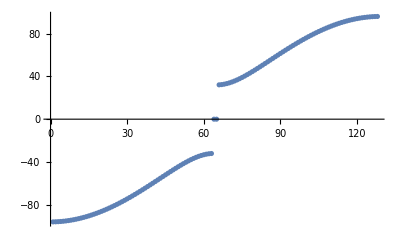

Kitaev_obc1.pdf

```mathematica
ListPlot[Sort[Eigenvalues[Hedge[0]/.{μ->0.5,Δ->1}]]]
Export["Kitaev_obc1.pdf",%]
```

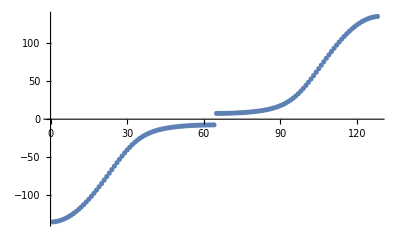

Kitaev_obc2.pdf

```mathematica
ListPlot[Sort[Eigenvalues[Hedge[π/2]/.{μ->0.5,Δ->1}]]]
Export["Kitaev_obc2.pdf",%]
```

```mathematica
ListPlot[Sort[Eigenvalues[Hedge[π]/.{μ->0.5,Δ->1}]]]
Export["Kitaev_obc3.pdf",%]
```

-Graphics-

Kitaev_obc3.pdf